300000000

6.626×10^-34

1.38×10^-23

General::munfl: 7.66399×10^17 1.1406721675×10^-34025 is too small to represent as a normalized machine number; precision may be lost.

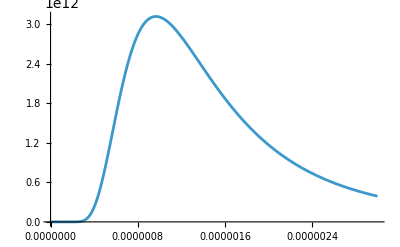

```mathematica
ClearAll[c,h,k,lambda, R]
c=3*10^8;
h=6.626*10^(-34);
k=1.38*10^(-23);

R[lambda_, t_]:=2 Pi c^2 h/lambda^5/(Exp[h c/(lambda k t)]-1)
Plot[R[x, 3000], {x, 0, 3 10^(-6)}]
```